## The pendulum A Physicist’s Guide to Mathematica, 2e, Patrick T. Tam F. I. Giasemis

### The plane pendulum

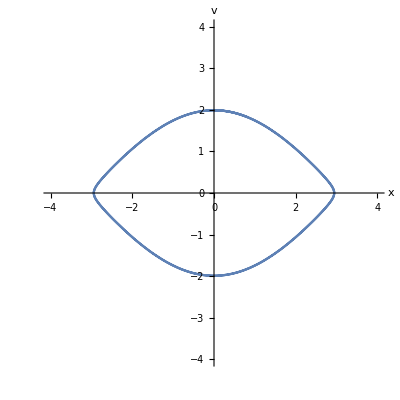

```mathematica
ClearAll["Global`*"]
points1=NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]],x[0]==0,v[0]==2-.01},{x,v},{t,0,30}];
ParametricPlot[Evaluate[{x[t],v[t]}/.points1],{t,0,30},PlotRange->{-4,4},AxesLabel->{"x","v"}]
```

### The damped pendulum

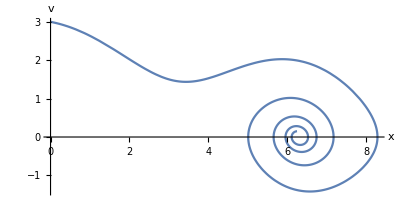

```mathematica
points2=NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-.2v[t],x[0]==0,v[0]==3},{x,v},{t,0,30}];
ParametricPlot[Evaluate[{x[t],v[t]}/.points2],{t,0,30},PlotRange->Full,AxesLabel->{"x","v"}]
```

### The damped, driven pendulum

```mathematica
{a,F,ω}={0.2,0.52,.694};
cycles=50;
x0=0.8;v0=0.8;
sol3=NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-a v[t]+F Cos[ω t],x[0]==x0,v[0]==v0},{x,v},{t,0,cycles (2Pi/ω)},MaxSteps->20000];
```

#### ParametricPlot[...] not useful

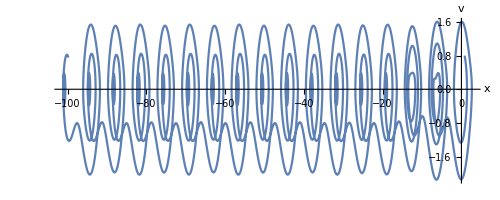

```mathematica
ParametricPlot[Evaluate[{x[t],v[t]}/.sol3],{t,0,cycles (2Pi/ω)},PlotRange->Full,AxesLabel->{"x","v"}]
```

#### Making x take values between -π and +π

```mathematica
reduce[x_]:=Mod[x,2Pi]/;Mod[x,2Pi]≤Pi;
reduce[x_]:=(Mod[x,2Pi]-2Pi)/;Mod[x,2Pi]>Pi;
(* lhs:=rhs/;test is a definition to be used only if test yields True. *)
```

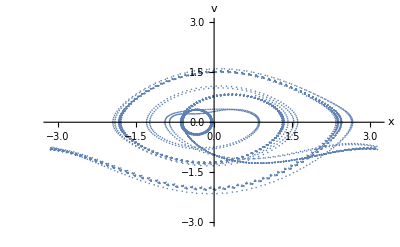

```mathematica
steps=100;
points3=Flatten[Table[{x[t],v[t]}/.sol3,{t,0,cycles(2Pi/ω),(1/steps)*(2Pi/ω)}],1];
newpoints3={reduce[#[[1]]],#[[2]]}&/@points3;
(* Map[f,expr] or f/@expr applies f to each element on the first level in expr. *)
ListPlot[newpoints3,PlotRange->{-3,3},AxesLabel->{"x","v"}]
```

#### Tests

```mathematica
Table[{x[t],v[t]}/.sol3,{t,0,cycles(2Pi/ω),(1/steps)*(2Pi/ω)}]
```

{{{0.8,0.8}},{{0.870906,0.765723}},{{0.938543,0.727871}},{{1.00261,0.686836}},{{1.06282,0.642983}},{{1.11896,0.596646}},{{1.17079,0.548115}},4988,{{-100.183,0.821514}},{{-100.109,0.817869}},{{-100.035,0.808964}},{{-99.9625,0.794993}},{{-99.8914,0.776202}},{{-99.8221,0.752877}}}
 |  |  |  |

```mathematica
Flatten[Table[{x[t],v[t]}/.sol3,{t,0,cycles(2Pi/ω),(1/steps)*(2Pi/ω)}],1]
```

{{0.8,0.8},{0.870906,0.765723},{0.938543,0.727871},{1.00261,0.686836},{1.06282,0.642983},{1.11896,0.596646},{1.17079,0.548115},4987,{-100.257,0.819765},{-100.183,0.821514},{-100.109,0.817869},{-100.035,0.808964},{-99.9625,0.794993},{-99.8914,0.776202},{-99.8221,0.752877}}
 |  |  |  |

```mathematica
points3[[1]][[1]]
```

0.8

```mathematica
reduce[points3[[1]]]
```

reduce[{0.8,0.8}]

#### Summary

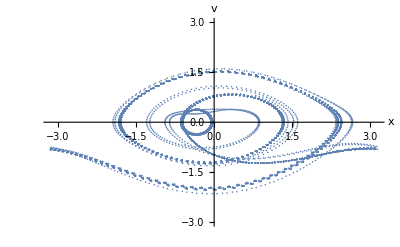

```mathematica
{a,F,ω}={0.2,0.52,.694};
cycles=100;
x0=0.8;v0=0.8;
sol3=NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-a v[t]+F Cos[ω t],x[0]==x0,v[0]==v0},{x,v},{t,0,cycles (2Pi/ω)},MaxSteps->20000];
steps=100;
points3=Flatten[Table[{x[t],v[t]}/.sol3,{t,0,cycles(2Pi/ω),(1/steps)*(2Pi/ω)}],1];
newpoints3={reduce[#[[1]]],#[[2]]}&/@points3;
(* Map[f,expr] or f/@expr applies f to each element on the first level in expr. *)
ListPlot[newpoints3,PlotRange->{-3,3},AxesLabel->{"x","v"}]
```

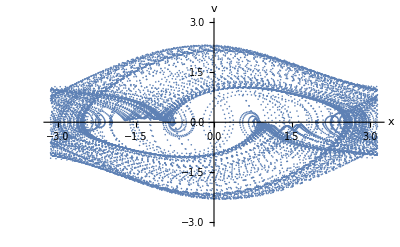

```mathematica
{a,F,ω}={0.5,1.15,2/3};
cycles=180;
x0=0.8;v0=0.8;
sol3=NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-a v[t]+F Cos[ω t],x[0]==x0,v[0]==v0},{x,v},{t,0,cycles (2Pi/ω)},MaxSteps->200000];
steps=100;
points3=Flatten[Table[{x[t],v[t]}/.sol3,{t,0,cycles(2Pi/ω),(1/steps)*(2Pi/ω)}],1];
newpoints3={reduce[#[[1]]],#[[2]]}&/@points3;
(* Map[f,expr] or f/@expr applies f to each element on the first level in expr. *)
ListPlot[newpoints3,PlotRange->{-3,3},AxesLabel->{"x","v"}]
```

### Plane and damped pendulum revisited

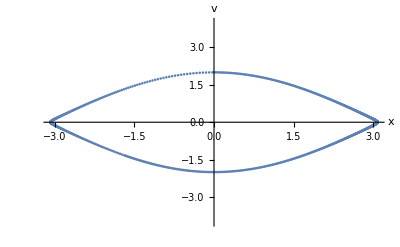

```mathematica
a=0.0;
x0=0;v0=2-.001;
sol4=NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-a v[t],x[0]==x0,v[0]==v0},{x,v},{t,0,30},MaxSteps->20000];
steps=1000;
points4=Flatten[Table[{x[t],v[t]}/.sol4,{t,0,30,(1/steps)*30}],1];
newpoints4={reduce[#[[1]]],#[[2]]}&/@points4;
(* Map[f,expr] or f/@expr applies f to each element on the first level in expr. *)
ListPlot[newpoints4,AxesLabel->{"x","v"},PlotRange->{-4,4}]
```

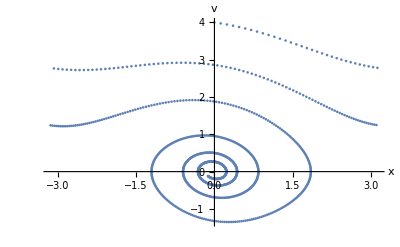

```mathematica
a=0.2;
x0=0;v0=4-.001;
sol4=NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-a v[t],x[0]==x0,v[0]==v0},{x,v},{t,0,30},MaxSteps->20000];
steps=1000;
points4=Flatten[Table[{x[t],v[t]}/.sol4,{t,0,30,(1/steps)*30}],1];
newpoints4={reduce[#[[1]]],#[[2]]}&/@points4;
(* Map[f,expr] or f/@expr applies f to each element on the first level in expr. *)
ListPlot[newpoints4,AxesLabel->{"x","v"}]
```

### Phase plane

```mathematica
points5=NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-.2v[t],x[0]==0,v[0]==3},{x,v},{t,0,30}];
points51=NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-.2v[t],x[0]==0,v[0]==2+0.1},{x,v},{t,0,30}];
points52=NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-.2v[t],x[0]==0,v[0]==2-0.1},{x,v},{t,0,30}];
points53=NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-.2v[t],x[0]==0,v[0]==1+0.1},{x,v},{t,0,30}];
points54=NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-.2v[t],x[0]==0,v[0]==4+0.1},{x,v},{t,0,30}];
(* AppendTo[points5,NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-.2v[t],x[0]==0,v[0]==2-0.1},{x,v},{t,0,30}]];
AppendTo[points5,NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-.2v[t],x[0]==0,v[0]==1},{x,v},{t,0,30}]]; *)
points5
```

{{x→InterpolatingFunction[{{0., 30.}}, <>],v→InterpolatingFunction[{{0., 30.}}, <>]}}

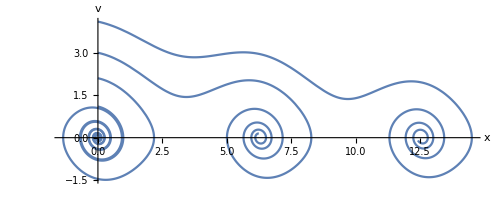

```mathematica
f1[t_]:=Evaluate[{x[t],v[t]}/.points5]
f2[t_]:=Evaluate[{x[t],v[t]}/.points51]
f3[t_]:=Evaluate[{x[t],v[t]}/.points52]
f4[t_]:=Evaluate[{x[t],v[t]}/.points53]
f5[t_]:=Evaluate[{x[t],v[t]}/.points54]
ParametricPlot[{f1[t],f2[t],f4[t],f5[t]},{t,0,30},AxesLabel->{"x","v"},PlotRange->Full,PlotStyle->ColorData[97,"ColorList"][[1]]]
```

#### Combining all the plots

```mathematica
flist={};
For[i=-4,i≤4,i+=1,
AppendTo[flist,Evaluate[{x[t],v[t]}/.NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-.2v[t],x[0]==0,v[0]==i},{x,v},{t,-4,30}]]]]
```

#### Damped pendulum phase plane

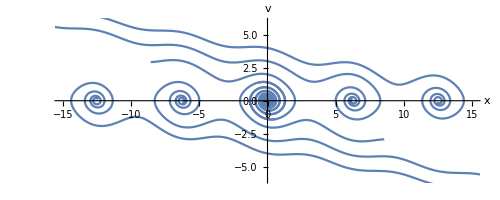

```mathematica
ParametricPlot[flist,{t,-4,30},AxesLabel->{"x","v"},PlotRange->{{-15,15},{-6,6}},PlotStyle->ColorData[97,"ColorList"][[1]]]
```

#### Plane pendulum phase plane

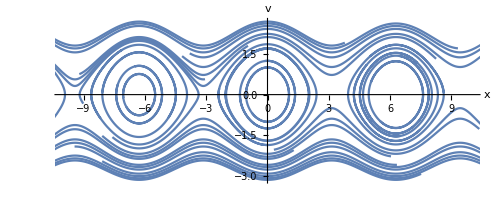

```mathematica
flist2={};
For[i=-2.5,i≤2.5,i+=1.1,
For[j=-10,j≤10,j+=3,
AppendTo[flist2,Evaluate[{x[t],v[t]}/.NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]],x[0]==j,v[0]==i},{x,v},{t,-2Pi,2Pi}]]]]]
ParametricPlot[flist2,{t,-2Pi,2Pi},AxesLabel->{"x","v"},PlotRange->{{-10,10},Full},PlotStyle->ColorData[97,"ColorList"][[1]],Axes->{-10,10}]
```

### Poincare section for the pendulum

-Graphics-

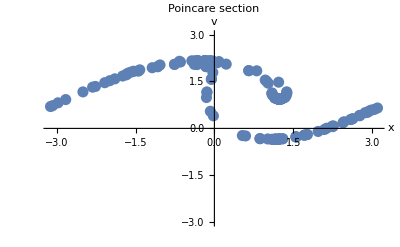

```mathematica
{a,F,ω}={0.5,1.15,2/3};
cycles=180;
x0=0.8;v0=0.8;
sol=NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-a v[t]+F Cos[ω t],x[0]==x0,v[0]==v0},{x,v},{t,0,cycles (2Pi/ω)},MaxSteps->200000];
steps=100;
points=Flatten[Table[{x[t],v[t]}/.sol,{t,0,cycles(2Pi/ω),(1/steps)*(2Pi/ω)}],1];
newpoints={reduce[#[[1]]],#[[2]]}&/@points;
poincare=Table[newpoints[[n]],{n,1+25steps,Length[newpoints],steps}];
ListPlot[newpoints,PlotRange->{-3,3},AxesLabel->{"x","v"}]
ListPlot[poincare,PlotRange->{-3,3},AxesLabel->{"x","v"},PlotStyle->PointSize[0.02],PlotLabel->"Poincare section"]
```

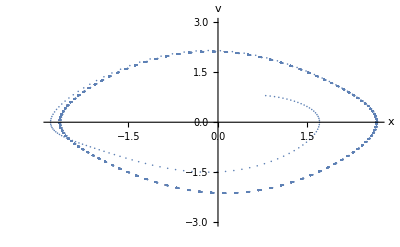

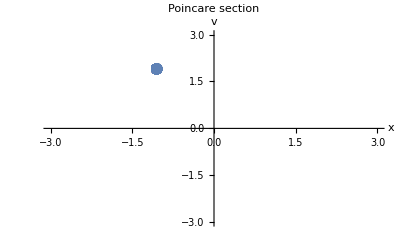

```mathematica
{a,F,ω}={.5,1.,2/3};
cycles=180;
x0=0.8;v0=0.8;
sol=NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-a v[t]+F Cos[ω t],x[0]==x0,v[0]==v0},{x,v},{t,0,cycles (2Pi/ω)},MaxSteps->200000];
steps=100;
points=Flatten[Table[{x[t],v[t]}/.sol,{t,0,cycles(2Pi/ω),(1/steps)*(2Pi/ω)}],1];
newpoints={reduce[#[[1]]],#[[2]]}&/@points;
poincare=Table[newpoints[[n]],{n,1+25steps,Length[newpoints],steps}];
ListPlot[newpoints,PlotRange->{-3,3},AxesLabel->{"x","v"}]
ListPlot[poincare,PlotRange->{{-3,3},{-3,3}},AxesLabel->{"x","v"},PlotStyle->PointSize[0.02],PlotLabel->"Poincare section"]
```